Fisher Matrix Code for the CSC method of measuring H(z)/H0 with LSST supernovae
Author: Miguel Quartin

## Preamble

```mathematica
SetDirectory[NotebookDirectory[]];
```

### Cosmology Preamble

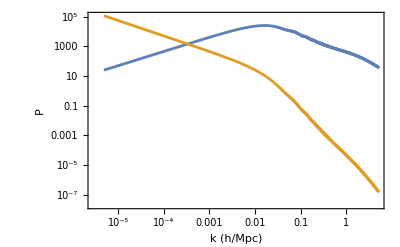

```mathematica
h=0.7;Ωm0fid=0.3;σintfid =0.13;
σvnonlinsq=(300/299792)^2; (* 300 km/s non-linear dispersion *)

power=Import["CAMB0.txt","Table"];

powerinterp=Interpolation[power];
powervv=power; (* radial velocity Power Spectrum *)
powervv[[All,2]]*=(1/powervv[[All,1]] 1/2998)^2;
powervvinterp=Interpolation[powervv];
powerplot=ListLogLogPlot[{powerinterp,powervvinterp},Frame->True,FrameLabel->{"k (h/Mpc)","P"}]
```

```mathematica
EE[z_]:=√(Ωm0fid (1+z)^3+(1-Ωm0fid));
(*dEdz[z_]=∂_z EE[z];*)

ff[z_]:=((Ωm0fid (1+z)^3)/EE[z]^2)^0.545;
G[zz_]:=Exp[-NIntegrate[ff[z]/(1+z),{z,0,zz}]]
```

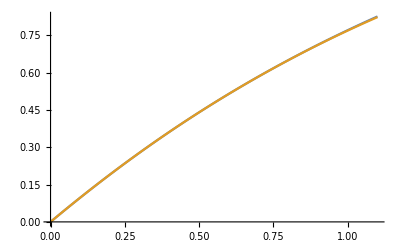

```mathematica
Clear[zz]
dCintegrandO6[z_]=Evaluate[Normal[Series[1/EE[z],{z,0,6}]]]; (* makes some evaluations faster *)
dC[zz_]:=NIntegrate[1/EE[z],{z,0,zz}];
dCO6[zz_]=Integrate[dCintegrandO6[z],{z,0,zz},Assumptions->zz>0];
Plot[{dC[z],dCO6[z]},{z,0,1.1}]
(*Plot[{dC[z]/dCO6[z]},{z,0,.8}]*)
```

### LSST Preamble

```mathematica
Dilday10Rate[z_]:=.26(1+z)^1.5 10^-4;
fidsnrate[z_]:=Dilday10Rate[z]h^-3/(1+z);
```

```mathematica
Cappellaro15Rate[z_]:=.21(1+z)^1.95 10^-4;
(*Dilday10Rate[z_]:=.26(1+z)^1.5 10^-4;*)

fidsnrate[z_]:=Cappellaro15Rate[z]h^-3/(1+z); (* corrects for obsframe and Mpc/h *)
Round[Map[fidsnrate[#]&,Range[.05,.75,.1]] 10^3,.0001]
Round[volLSSTbins={0.1339,0.8618,2.119,3.713,5.486,7.319,9.124,10.84} h^3 ,.001]
```

{0.0641,0.0699,0.0757,0.0814,0.0871,0.0928,0.0985,0.1042}

{0.046,0.296,0.727,1.274,1.882,2.51,3.13,3.718}

```mathematica
Δz=.1;{zmin,zmax}={0,.8};
zzvec=Range[zmin+Δz/2,zmax-Δz/2,Δz];
completenessLSSTvec5yΔz0p05=Import["completnessLSST5yr-Dz=0.05.txt","Table"];  (* From arxiv:1905.00746 *)
completenessSQΔz005=Interpolation[completenessLSSTvec5yΔz0p05];
completenessLSSTvec5yΔz0p1=Table[{zmin+.05,NIntegrate[ completenessSQΔz005[z],{z,zmin,zmin+Δz}]/NIntegrate[1,{z,zmin,zmin+Δz}]},{zmin,zmin,zmax,Δz}];
completenessSQΔz01=Interpolation[completenessLSSTvec5yΔz0p1]
nLSST5ySQΔz0p1=Map[5*fidsnrate[#]completenessSQΔz01[#]&,zzvec]

completeness20p[z_]:=0.2; (* constant 20% completeness *)
nLSST5y20pΔz0p1=Map[5*fidsnrate[#]completeness20p[#]&,zzvec]
```

InterpolatingFunction[…]

{0.0000127351,0.000036756,0.0000589194,0.0000563907,0.0000382788,0.0000123432,1.94594×10^-6,2.31753×10^-7}

{0.0000776737,0.0000812883,0.0000847489,0.0000880737,0.0000912774,0.0000943724,0.0000973691,0.000100276}

```mathematica
kminvecΔz0p05={{0.025,0.03468},{0.075,0.01837},{0.125,0.01338},{0.175,0.01089},{0.225,0.00938},{0.275,0.00835},{0.325,0.00761},{0.375,0.00704},{0.425,0.0066},{0.475,0.00624},{0.525,0.00595}};
kminvecΔz0p1={{0.05,0.01754},{0.15,0.00943},{0.25,0.00699},{0.35,0.0058},{0.45,0.00509},{0.55,0.00462},{0.65,0.0043},{0.75,0.00406},{0.85,0.00387},{0.95,0.00373}};

kminvecLSSTΔz0p05=kminvecΔz0p05;
kminvecLSSTΔz0p1=kminvecΔz0p1;
```

## CSC

Choose which LSST nSN and which kmax to use

```mathematica
nSNvec = nLSST5y20pΔz0p1;
```

```mathematica
nSNvec =nLSST5ySQΔz0p1;
```

```mathematica
kmax=0.1;
```

```mathematica
kmax=0.3;
```

### CSC Preamble

```mathematica
(* dC are distances × H0 *)
```

```mathematica
fskyLSST=18000/(180/π)^2 1./(4π);
Gvec=Map[G,zzvec];
fvec=Map[ff,zzvec];
bfid=1.6; 
βfidvec=fvec/bfid;
Pfidvec[k_]:=bfid^2 Gvec^2 nSNvec powerinterp[k]; (* fid Pmm(k) in (h/Mpc)^3*)
dPdkfidvec[k_]:=bfid^2 Gvec^2 nSNvec powerinterp'[k];
Hr[z_]:=2998^-1 EE[z]; (* in h/Mpc *)
dCoverdH[z_]:=dCO6[z];
ΔV[z_]:=2998^3 4π fskyLSST NIntegrate[(dCoverdH[zz])^2/EE[zz],{zz,z-Δz/2,z+Δz/2}]
Round[ΔVvec=Map[ΔV,zzvec],10.^6]
Round[1000 nSNvec,.001]
```

{4.6×10^7,2.96×10^8,7.27×10^8,1.273×10^9,1.882×10^9,2.51×10^9,3.128×10^9,3.715×10^9}

Round[1000 nSNvec,0.001]

### LSST CSC method σv, σv free or constant

Parameter order:
P(k1), β(k1), ... , P(kn), β(kn), σv, σδ, η
σv, σδ are in principle kept as free parameters in each redshift bin, but as default in the results they are assumed fixed (i.e., NOT marginalized over)

```mathematica
Clear[Sδ,Sv,Bbar,Abar,Cab,CabInv,NvAbarsqP,NδBbarsqP,kmin]
σδfid=4.24;σvfid=13;
(*Sδ[k_,μ_,σδ_]:=1/(√(1+1/2(k μ σδ)^2)); Sv[k_,σv_]:=Sin[k σv]/(k σv);*)
Sδ[kr_,μ_,σδ_,η_]:=1/(√(1+1/2(kr μ η σδ)^2)); Sv[kr_,μr_,σv_,η_]:=Sin[kr σv √(μr^2(η^2-1)+1)]/(kr σv √(μr^2(η^2-1)+1));
Abar[kr_,μr_,β_,σv_,η_,z_]:=(Hr[z] Sv[kr,μr,σv,η])/(kr (1+z))(β μr η^2)/(μr^2(η^2-1)+1);
Bbar[kr_,μr_,β_,σδ_,η_]:=(1+(β η^2 μr^2)/(μr^2(η^2-1)+1))Sδ[kr,μr,σδ,η];
σveffsq[z_]:=(Log[10]/5 σintfid)^2(dCoverdH[z]/(dCoverdH[z] - (1+z)/EE[z]))^2+σvnonlinsq;
NvAbarsqP[kr_,μr_,P_,β_,σv_,η_,z_]:=P Abar[kr,μr,β,σv,η,z]^2+σveffsq[z];
NδBbarsqP[kr_,μr_,P_,β_,σδ_,η_]:=P Bbar[kr,μr,β,σδ,η]^2+1;
Cab[kr_,μr_,P_,β_,σv_,σδ_,η_,z_]:={{NδBbarsqP[kr,μr,P,β,σδ,η],P Abar[kr,μr,β,σv,η,z] Bbar[kr,μr,β,σδ,η]},{P Abar[kr,μr,β,σv,η,z] Bbar[kr,μr,β,σδ,η],NvAbarsqP[kr,μr,P,β,σv,η,z]}}
CabInv[kr_,μr_,P_,β_,σv_,σδ_,η_,z_]:=Inverse[Cab[kr,μr,P,β,σv,σδ,η,z]];

σηfun[FM_]:=Module[{full,fixed,covmat,covmat2},
covmat2=Inverse[Drop[FM,{-3,-2},{-3,-2}]];fixed=√covmat2[[-1,-1]];
fixed
];
```

```mathematica
(* Using du = 1/40 and kmax = 0.1 (0.3) the code below takes around 3 (8) minutes to run  *)
Clear[kr,Pf,βf,ηf,dPfdη,Fbar,z];
du=1/40; (* 1/40 for very high precision; 1/10 for high precision *)

(*{μvec=Range[-1+du/2,1-du/2,du]; multfact=1;};*)
{μvec=Range[du/2,1-du/2,du]; multfact=2;}; (* FM is symmetric in μ *)

Fbar[p1_,p2_,Pf_,βf_,ηf_,z_]:=multfact(1/2)du Total[Map[Tr[(D[Cab[kr,#,P[η],β,σv,σδ,η,z],p1]/.{P[η]->Pf,β->βf,σv->σvfid,σδ->σδfid,η->ηf,P'[η]->dPfdη[#]}).CabInv[kr,#,Pf,βf,σvfid,σδfid,ηf,z].(D[Cab[kr,#,P[η],β,σv,σδ,η,z],p2]/.{P[η]->Pf,β->βf,σv->σvfid,σδ->σδfid,η->ηf,P'[η]->dPfdη[#]}).CabInv[kr,#,Pf,βf,σvfid,σδfid,ηf,z]]&,μvec]];

AbsoluteTiming[Monitor[FMvec=
Table[
zz=zzvec[[iz]];
kmin=kminvecΔz0p1[[iz,2]];Δk= 2π/ΔVvec[[iz]]^(1/3);
(* k starts at kmax and go down until kmin *)
kbins=Range[kmax,kmin,-Δk];kbins=Join[kbins,{kmin}];
Δklast=kbins[[-2]]-kmin; (* the last kbin is smaller in order not to go below kmin *)
kvec=MovingAverage[kbins,2]; (* central ks *)
FMlength=2Length[kvec]+3;
(*Print["nk = "<>ToString[FMlength]<>"; {kmin, kmineff, kmax} = "<>ToString[{kmin, kbins[[-1]], kmax}]];*)
FM=Table[0,{i,FMlength},{j,FMlength}];
FMtot=FM;
βf=βfidvec[[iz]];ηf=1;
Do[
FM=Table[0,{i,FMlength},{j,FMlength}];
kr=kvec[[ik]];(*α[μr_]:=√(μr^2(ηf^2-1)+1)(1/ηf);*)
Pf=Pfidvec[kr][[iz]];dPfdη[μr_]:=(dPdkfidvec[kr][[iz]] kr ηf μr^2)/(√(μr^2(ηf^2-1)+1));
If[ik==Length[kvec],VVk=Δklast/Δk(kr^2 ΔVvec[[iz]]^(2/3))/(2π),VVk=(kr^2 ΔVvec[[iz]]^(2/3))/(2π)];

FM[[2ik-1,2ik-1]]=Fbar[P[η],P[η],Pf,βf,ηf,zz];
FM[[2ik-1,2ik]]=Fbar[P[η],β,Pf,βf,ηf,zz];
FM[[2ik,2ik-1]]=FM[[2ik-1,2ik]];
FM[[2ik,2ik]]=Fbar[β,β,Pf,βf,ηf,zz];

FM[[2ik-1,-1]]=Fbar[P[η],η,Pf,βf,ηf,zz];
FM[[2ik-1,-2]]=Fbar[P[η],σδ,Pf,βf,ηf,zz];
FM[[2ik-1,-3]]=Fbar[P[η],σv,Pf,βf,ηf,zz];
FM[[2ik,-1]]=Fbar[β,η,Pf,βf,ηf,zz];
FM[[2ik,-2]]=Fbar[β,σδ,Pf,βf,ηf,zz];
FM[[2ik,-3]]=Fbar[β,σv,Pf,βf,ηf,zz];

FM[[-1,2ik-1]]=FM[[2ik-1,-1]];
FM[[-2,2ik-1]]=FM[[2ik-1,-2]];
FM[[-3,2ik-1]]=FM[[2ik-1,-3]];
FM[[-1,2ik]]=FM[[2ik,-1]];
FM[[-2,2ik]]=FM[[2ik,-2]];
FM[[-3,2ik]]=FM[[2ik,-3]];

FM[[-3,-3]]=Fbar[σv,σv,Pf,βf,ηf,zz];
FM[[-3,-2]]=Fbar[σv,σδ,Pf,βf,ηf,zz];
FM[[-3,-1]]=Fbar[σv,η,Pf,βf,ηf,zz];
FM[[-2,-2]]=Fbar[σδ,σδ,Pf,βf,ηf,zz];
FM[[-2,-1]]=Fbar[σδ,η,Pf,βf,ηf,zz];
FM[[-2,-3]]=FM[[-3,-2]];
FM[[-1,-3]]=FM[[-3,-1]];
FM[[-1,-2]]=FM[[-2,-1]];
FM[[-1,-1]]=Fbar[η,η,Pf,βf,ηf,zz];
FMtot+=VVk FM;
,{ik,Length[kvec]}];
FMtot
,{iz,1,Length[zzvec]}];,{iz,ik,Length[kvec]}]]
```

{247.991,Null}

```mathematica
Round[Map[σηfun,FMvec],.001]
```

{0.103,0.066,0.049,0.039,0.032,0.028,0.025,0.023}

LSST 20%, bfid=1.6
σv and σδ completely fixed (known a priori)
kmax = 0.1 → σH / H = {0.132,0.089,0.076,0.069,0.063,0.058,0.054,0.051}
kmax = 0.2 → σH / H = {0.107,0.071,0.056,0.046,0.039,0.034,0.031,0.028}
kmax = 0.3 → σH / H = {0.103,0.065,0.048,0.038,0.032,0.028,0.025,0.023}

LSST SQ, bfid=1.6
σv and σδ completely fixed (known a priori)
kmax = 0.1 → σH / H = {0.39,0.14,0.092,0.086,0.099,0.20,1.0,7.8}
kmax = 0.2 → σH / H = {0.35,0.12,0.069,0.060,0.067,0.15,0.76,5.9}
kmax = 0.3 → σH / H = {0.34,0.109,0.061,0.051,0.058,0.131,0.685,5.377}

### Tests

```mathematica
FMtemp=FMvec[[1]];
{PositiveDefiniteMatrixQ[FMtemp],Det[FMtemp]}
Round[FMtemp,1]//MatrixForm
covmat=Inverse[FMtemp];
diag=√Diagonal[covmat];
corrmat=covmat/Outer[Times,diag,diag];
Round[corrmat,.1][[;;-1,;;-1]]//MatrixForm
Round[Diagonal[covmat],.0001]
σηsq=covmat[[-1,-1]];
ση=√σηsq
```

{True,6.672×10^8}

(50 | 38 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -28
38 | 80 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | -31
0 | 0 | 22 | 26 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -8
0 | 0 | 26 | 112 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -3
0 | 0 | 0 | 0 | 10 | 17 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 17 | 141 | 0 | 0 | 0 | 0 | -1 | 0 | 21
0 | 0 | 0 | 0 | 0 | 0 | 3 | 10 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 10 | 190 | 0 | 0 | 0 | 0 | 38
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 160 | 0 | 0 | 46
0 | -1 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
-28 | -31 | -8 | -3 | 0 | 21 | 0 | 38 | 1 | 46 | 0 | 1 | 105)

(1. | -0.6 | 0.3 | -0.6 | 0.1 | -0.6 | 0. | -0.6 | 0. | -0.6 | -0.6 | -0.6 | 0.
-0.6 | 1. | -0.2 | 1. | 0. | 1. | 0.1 | 1. | 0. | 0.9 | 1. | 1. | -0.1
0.3 | -0.2 | 1. | -0.2 | 0.1 | -0.2 | 0. | -0.2 | 0. | -0.2 | -0.2 | -0.2 | -0.1
-0.6 | 1. | -0.2 | 1. | 0. | 1. | 0.1 | 1. | 0. | 0.9 | 1. | 1. | -0.1
0.1 | 0. | 0.1 | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0.1 | -0.1
-0.6 | 1. | -0.2 | 1. | 0. | 1. | 0. | 1. | 0. | 0.9 | 1. | 1. | -0.1
0. | 0.1 | 0. | 0.1 | 0. | 0. | 1. | 0. | 0. | 0. | 0.1 | 0.1 | 0.1
-0.6 | 1. | -0.2 | 1. | 0. | 1. | 0. | 1. | 0. | 0.9 | 1. | 1. | -0.2
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | -0.1 | 0. | 0. | 0.
-0.6 | 0.9 | -0.2 | 0.9 | 0. | 0.9 | 0. | 0.9 | -0.1 | 1. | 0.9 | 0.9 | -0.3
-0.6 | 1. | -0.2 | 1. | 0. | 1. | 0.1 | 1. | 0. | 0.9 | 1. | 1. | -0.1
-0.6 | 1. | -0.2 | 1. | 0.1 | 1. | 0.1 | 1. | 0. | 0.9 | 1. | 1. | -0.2
0. | -0.1 | -0.1 | -0.1 | -0.1 | -0.1 | 0.1 | -0.2 | 0. | -0.3 | -0.1 | -0.2 | 1.)

{0.0741,12.8119,0.0807,5.1038,0.1369,1.6187,0.4106,0.3508,2.6327,0.0586,68008.,26761.1,0.0284}

0.168544

### Fit for ΔH/H vs. ΔD_L/D_L

```mathematica
σHoverH=Round[Map[σηfun,FMvec],.001]
```

{0.132,0.089,0.076,0.069,0.063,0.059,0.055,0.052}

```mathematica
NSNvec=Round[nSNvec ΔVvec]  (* N is number density times volume *)
degradation=1.22;
Round[σDLoverDL=degradation(Log[10]/5)σintfid/√NSNvec,.00001]
σHoverH={0.1319,0.0894,0.0763,0.0689,0.0633,0.0587,0.0548,0.0516} (* new result*)
σHoverH/σDLoverDL
```

{2946,20669,54999,103683,163977,233042,308206,387087}

{0.00135,0.00051,0.00031,0.00023,0.00018,0.00015,0.00013,0.00012}

{0.1319,0.0894,0.0763,0.0689,0.0633,0.0587,0.0548,0.0516}

{98.0195,175.974,244.993,303.755,350.951,387.977,416.536,439.547}

{a→529.511,b→0.552044}

{a→108.426,b→484.482}

{a→565.289,b→0.469091,c→-45.6331}

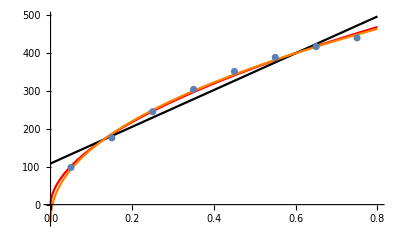

```mathematica
datafit=Thread[{zzvec,σHoverH/σDLoverDL}];
fit1=FindFit[datafit,{a z^b},{a,b},z]
fit2=FindFit[datafit,{a +b z},{a,b},z]
fit3=FindFit[datafit,{a z^b+c,100>c,a<700,b>0},{a,b,c},z]
Show[Plot[{a z^b/.fit1,a+b z /.fit2,a z^b+c/.fit3},{z,0,.8},PlotStyle->{Red,Black,Orange}],ListPlot[datafit]]
```

```mathematica
σHoverH/σDLoverDL
```

{98.0195,175.974,244.993,303.755,350.951,387.977,416.536,439.547}

### Plots on the errors on P (k)

```mathematica
Round[√Diagonal[Inverse[FMvec[[1]]]],.01]
%[[1;;-2;;2]]
```

{0.05,0.81,0.05,0.75,0.05,0.7,0.06,0.65,0.06,0.59,0.07,0.53,0.08,0.47,0.09,0.41,0.1,0.34,0.12,0.27,0.14,0.22,0.16,0.18,0.22,0.13,0.31,0.11,0.49,0.09,1.06,0.08,5.82,0.25,4.98,5.89,0.12}

{0.05,0.05,0.05,0.06,0.06,0.07,0.08,0.09,0.1,0.12,0.14,0.16,0.22,0.31,0.49,1.06,5.82,4.98}

```mathematica
color1=RGBColor[65/255,144/255,210/255]
color2=RGBColor[138/255,32/255,13/255]
color3=RGBColor[65/255,144/255,10/255]
```

RGBColor[Rational[13, 51], Rational[48, 85], Rational[14, 17]]

RGBColor[Rational[46, 85], Rational[32, 255], Rational[13, 255]]

RGBColor[Rational[13, 51], Rational[48, 85], Rational[2, 51]]

```mathematica
kvecfun[iz_]:=Module[{},
kmin=kminvecΔz0p1[[iz,2]];Δk= 2π/ΔVvec[[iz]]^(1/3);
kbins=Range[kmax,kmin,-Δk];kbins=Join[kbins,{kmin}];
MovingAverage[kbins,2]];
σPfun[FM_]:=Module[{covmat2},
covmat2=Inverse[Drop[FM,{-3,-2},{-3,-2}]];
√(Diagonal[covmat2][[1;;-2;;2]])
];
```

```mathematica
kvecfun[2]
σPfun[FMvec[[2]]]
```

{0.295284,0.285852,0.27642,0.266988,0.257556,0.248124,0.238692,0.22926,0.219828,0.210396,0.200964,0.191532,0.1821,0.172668,0.163236,0.153804,0.144372,0.13494,0.125508,0.116076,0.106644,0.0972115,0.0877795,0.0783475,0.0689154,0.0594834,0.0500514,0.0406194,0.0311873,0.0217553,0.0132347}

{0.0243425,0.0252546,0.0262692,0.0273672,0.0285232,0.0297401,0.0310726,0.0326175,0.0344587,0.0366013,0.0389492,0.0413861,0.0439303,0.0468316,0.0505036,0.0552896,0.0611779,0.0677324,0.0744734,0.0816855,0.0908427,0.10417,0.123399,0.14808,0.176175,0.208784,0.256001,0.341636,0.507451,0.826341,1.51615}

```mathematica
nσ=1;
pskz[k_,iz_]:=Pfidvec[k][[iz]]; 
dataerr[iz_]:=MapThread[Around,{Map[Pfidvec[#][[iz]]&,kvecfun[iz]],nσ σPfun[FMvec[[iz]]]}];
datafull[iz_]:=Thread[{kvecfun[iz],dataerr[iz]}];

pplot[iz_]:=Plot[k^0 pskz[k,iz],{k,0.35,0.001},Frame->True,FrameLabel->{"k","P(k)"},BaseStyle->{16,FontFamily->"Times"},PlotStyle->color1];
plogplot[iz_]:=LogLogPlot[k^0 pskz[k,iz],{k,0.35,0.003},Frame->True,FrameLabel->{"k","P(k)"},BaseStyle->{16,FontFamily->"Times"},PlotStyle->If[iz≤4,color1,Black],FrameTicks->{{Automatic,Automatic},{Join[Table[{i,""},{i,.001,.01,.001}],Table[{i,""},{i,.01,.1,.01}],{.01,.02,.05,.1,.2,{.3,""}}],Automatic}}];
```

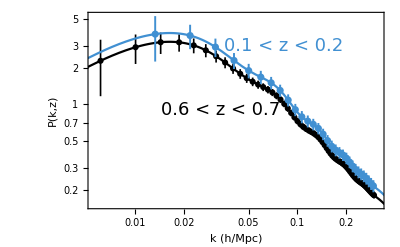

```mathematica
Ptextz1=Graphics[{Text[Style["0.1 < z < 0.2",18,color1],{-2.5,1.1}]}];
Ptextz2=Graphics[{Text[Style["0.6 < z < 0.7",18,Black],{-3.4,-.1}]}];
sPkmax03=Show[plogplot[7],
ListLogLogPlot[datafull[7],Joined->False,IntervalMarkersStyle->{Black,Thickness[.003]},PlotStyle->Black],
plogplot[2],
ListLogLogPlot[datafull[2],Joined->False,IntervalMarkersStyle->{color1,Thickness[.0035]},PlotStyle->color1],Ptextz1,Ptextz2,
Frame->True,FrameStyle->19,PlotRange->{{-5.2,-1.15},All},(*{{-4.85,-1.15},{6.2,10.}},*)FrameLabel->{"k (h/Mpc)","P(k,z)"}]
```

### Error on H as a function of n_SN

```mathematica
ndensvec=Table[10^-i,{i,3,6,.11}]
Dimensions[ndensvec]
```

```mathematica
(* Using du = 1/20 and kmax = 0.1 the code below takes around 15 minutes to run  *)

Clear[kr,Pf,βf,ηf,dPfdη,Fbar,z];
kmax=0.1;
Pprimefact=1;
du=1/20;

(*{μvec=Range[-1+du/2,1-du/2,du]; multfact=1;};*)
{μvec=Range[du/2,1-du/2,du]; multfact=2;};

Fbar[p1_,p2_,Pf_,βf_,ηf_,z_]:=multfact(1/2)du Total[Map[Tr[(D[Cab[kr,#,P[η],β,σv,σδ,η,z],p1]/.{P[η]->Pf,β->βf,σv->σvfid,σδ->σδfid,η->ηf,P'[η]->dPfdη[#]}).CabInv[kr,#,Pf,βf,σvfid,σδfid,ηf,z].(D[Cab[kr,#,P[η],β,σv,σδ,η,z],p2]/.{P[η]->Pf,β->βf,σv->σvfid,σδ->σδfid,η->ηf,P'[η]->dPfdη[#]}).CabInv[kr,#,Pf,βf,σvfid,σδfid,ηf,z]]&,μvec]];

AbsoluteTiming[Monitor[herrornSN=
Table[
Table[
zz=zzvec[[iz]];

Pfidvec[k_]:=bfid^2 Gvec^2 ndensvec[[in]] powerinterp[k]; (* fid Pmm(k) in (h/Mpc)^3*)
dPdkfidvec[k_]:=bfid^2 Gvec^2 ndensvec[[in]] powerinterp'[k];

kmin=kminvecΔz0p1[[iz,2]];Δk= 2π/ΔVvec[[iz]]^(1/3);
(* k starts at kmax and go down until kmin *)
kbins=Range[kmax,kmin,-Δk];kbins=Join[kbins,{kmin}];
Δklast=kbins[[-2]]-kmin; (* the last kbin is smaller in order not to go below kmin *)
kvec=MovingAverage[kbins,2]; (* central ks *)
FMlength=2Length[kvec]+3;
FM=Table[0,{i,FMlength},{j,FMlength}];
FMtot=FM;
βf=βfidvec[[iz]];ηf=1;
Do[
FM=Table[0,{i,FMlength},{j,FMlength}];
kr=kvec[[ik]];
Pf=Pfidvec[kr][[iz]];dPfdη[μr_]:=(Pprimefact dPdkfidvec[kr][[iz]] kr ηf μr^2)/(√(μr^2(ηf^2-1)+1));
If[ik==Length[kvec],VVk=(Δklast/Δk)((kr^2 ΔVvec[[iz]]^(2/3))/(2π)),VVk=(kr^2 ΔVvec[[iz]]^(2/3))/(2π)];

FM[[2ik-1,2ik-1]]=Fbar[P[η],P[η],Pf,βf,ηf,zz];
FM[[2ik-1,2ik]]=Fbar[P[η],β,Pf,βf,ηf,zz];
FM[[2ik,2ik-1]]=FM[[2ik-1,2ik]];
FM[[2ik,2ik]]=Fbar[β,β,Pf,βf,ηf,zz];

FM[[2ik-1,-1]]=Fbar[P[η],η,Pf,βf,ηf,zz];
FM[[2ik,-1]]=Fbar[β,η,Pf,βf,ηf,zz];

FM[[-1,2ik-1]]=FM[[2ik-1,-1]];
FM[[-2,2ik-1]]=FM[[2ik-1,-2]];
FM[[-3,2ik-1]]=FM[[2ik-1,-3]];
FM[[-1,2ik]]=FM[[2ik,-1]];
FM[[-2,2ik]]=FM[[2ik,-2]];
FM[[-3,2ik]]=FM[[2ik,-3]];

FM[[-2,-3]]=FM[[-3,-2]];
FM[[-1,-3]]=FM[[-3,-1]];
FM[[-1,-2]]=FM[[-2,-1]];
FM[[-1,-1]]=Fbar[η,η,Pf,βf,ηf,zz];
FMtot+=VVk FM;
,{ik,Length[kvec]}];
covmat2=Inverse[Drop[FMtot,{-3,-2},{-3,-2}]];
{ndensvec[[in]],√covmat2[[-1,-1]]}
,{iz,1,8}]
,{in,Length[ndensvec]}]
,{in,iz,ik,Length[kvec]}];]
```

{490.272,Null}

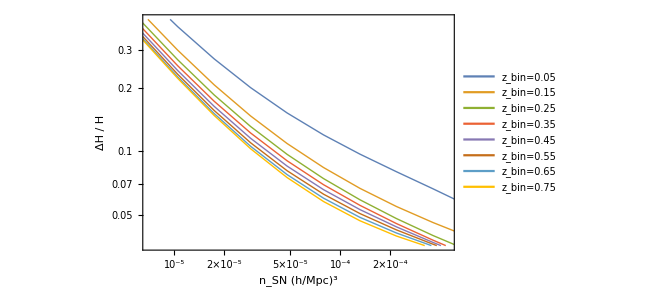

```mathematica
legsize=15;
errplot=ListLogLogPlot[Table[herrornSN[[All,i]],{i,1,Length[zzvec]}],Joined->True,Frame->True,FrameStyle->21,FrameLabel->{"n_SN (h/Mpc)^3","ΔH / H"},PlotLegends->Placed[LineLegend[{Style["z_bin=0.05",legsize],Style["z_bin=0.15",legsize],Style["z_bin=0.25",legsize],Style["z_bin=0.35",legsize],Style["z_bin=0.45",legsize],Style["z_bin=0.55",legsize],Style["z_bin=0.65",legsize],Style["z_bin=0.75",legsize]},LegendLayout->{"Column",1},LegendMarkerSize->{25,3},LegendFunction->(Framed[#,Background->Directive[White, Opacity[.6]],FrameStyle->Gray]&)],{{.72,.24},{0,0}}],
PlotStyle->Thick,ImageSize->480,
FrameTicks->{{Automatic,Automatic},{{{3 10.^-6,"3.10^-6"},{10.^-5,"10^-5"},{3 10.^-5,"3.10^-5"},{10.^-4,"10^-4"},{3 10.^-4,"3.10^-4"}},Automatic}},GridLines->{Thread[{{3 10.^-6,10.^-5,3 10.^-5,10.^-4,3 10.^-4},{Gray,Gray,Gray,Gray,Gray}}],Automatic},
PlotRange->{{7 10^-6,4.5 10^-4},{.036,.42}}]
```